```mathematica
p = 1/2;
M = Power[(2/(1-p))*(1+(2/(1-p))),1/(p-1)];
```

```mathematica
rad[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
```

```mathematica
rad2[x_,y_,z_]:=x^2+y^2+z^2;
$Assumptions=x^2+y^2+z^2>0;
```

```mathematica
w[x_,y_,z_]:=M*Power[rad2[x,y,z],1/(1-p)];
```

```mathematica
FullSimplify[Laplacian[w[x,y,z],{x,y,z}]-Power[w[x,y,z],p]]
```

0

```mathematica
M2D = Power[(2/(1-p))*((2/(1-p))),1/(p-1)];
```

```mathematica
rad22d[x_,y_]:=x^2+y^2;
```

```mathematica
w2d[x_,y_]:=M2D*Power[rad22d[x,y],1/(1-p)];
```

```mathematica
FullSimplify[Laplacian[w2d[x,y],{x,y}]-Power[w2d[x,y],p]]
```

0

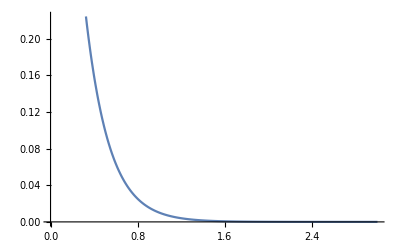

```mathematica
Plot[Power[.1,2*x], {x,0,3}]
```

```mathematica
.1*.1
```

0.01

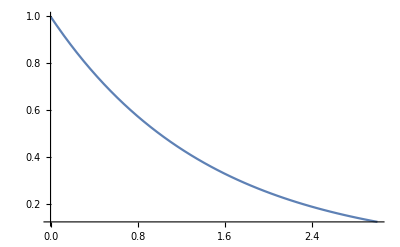

```mathematica
Plot[Power[.5,x], {x,0,3}]
```